```mathematica
SetDirectory[NotebookDirectory[]]
list=FileNames[]
```

/Users/eduardogrossi/langevinA/ModelA-Beuler

{.DS_Store,.ipynb_checkpoints,langev,langeva1,Makefile 15.00.54,metropolis,modelA-Beuler,ModelA-Beuler.cxx,ModelA-Beuler.exe,ModelA-Beuler.o,modelA-Beuler.zip,outputH0.h5,plot.ipynb 15.00.54,plot.pdf,plot.py,run.py,Untitled-2.nb}

```mathematica
listlangev=Table["langeva1/H"<>ToString[i]<>".h5",{i,0,19}]
```

{langeva1/H0.h5,langeva1/H1.h5,langeva1/H2.h5,langeva1/H3.h5,langeva1/H4.h5,langeva1/H5.h5,langeva1/H6.h5,langeva1/H7.h5,langeva1/H8.h5,langeva1/H9.h5,langeva1/H10.h5,langeva1/H11.h5,langeva1/H12.h5,langeva1/H13.h5,langeva1/H14.h5,langeva1/H15.h5,langeva1/H16.h5,langeva1/H17.h5,langeva1/H18.h5,langeva1/H19.h5}

```mathematica
listmetropolis=Table["metropolis/H"<>ToString[i]<>"_averages.txt",{i,0,19}]
```

{metropolis/H0_averages.txt,metropolis/H1_averages.txt,metropolis/H2_averages.txt,metropolis/H3_averages.txt,metropolis/H4_averages.txt,metropolis/H5_averages.txt,metropolis/H6_averages.txt,metropolis/H7_averages.txt,metropolis/H8_averages.txt,metropolis/H9_averages.txt,metropolis/H10_averages.txt,metropolis/H11_averages.txt,metropolis/H12_averages.txt,metropolis/H13_averages.txt,metropolis/H14_averages.txt,metropolis/H15_averages.txt,metropolis/H16_averages.txt,metropolis/H17_averages.txt,metropolis/H18_averages.txt,metropolis/H19_averages.txt}

```mathematica
datalangev=Import[#,"/Timestepsolution/<phi>"]&/@listlangev
```

{{{0.230916,-2.64573,-3.58414,-3.25893,5.52448},2999,{339.868,-4331.78,229.525,644.354,4398.6}},18,{1}}
 |  |  |  |

```mathematica
datametro=Import[#,"Table"]&/@listmetropolis
```

{{{2087.22,2096.24,2117.93,2060.51,4181.16},498,{2456.76,816.922,2324.23,2512.95,4291.86}},{{1},498,{1}},16,{1},{1}}
 |  |  |  |

```mathematica
averegelangev[list_,start_,deltat_]:=
Block[
{mean,variance},
mean=Table[Total[list[[j,start;;All,i]]]/(Length[list[[j,start;;All,i]]]),{j,1,20},{i,1,5}];
variance=Table[Total[list[[j,start;;All,i]]*list[[j,start;;All,i]]]/(Length[list[[j,start;;All,i]]]),{j,1,20},{i,1,5}];
<|"mean"->mean,"variance"->(variance)-mean*mean,"error"->Sqrt[(variance)-mean*mean]|>]
```

```mathematica
averegemetro[list_]:=Block[
{mean,variance},
mean=Table[Total[list[[j,All,i]]]/(Length[list[[j,All,i]]]),{j,1,20},{i,1,5}];
variance=Table[Total[list[[j,All,i]]*list[[j,All,i]]]/(Length[list[[j,All,i]]]),{j,1,20},{i,1,5}];
<|"mean"->mean,"variance"->(variance)-mean*mean,"error"->Sqrt[(variance)-mean*mean]|>]
```

```mathematica
Dimensions[datametro]
```

{20,500,5}

```mathematica
Dimensions[data]
```

{20,1502,5}

```mathematica
Manipulate[ListPlot[datametro[[i,All,5]],PlotRange->All],{i,1,20}]
```

Part::pkspec1: The expression 14.62 cannot be used as a part specification.

ListPlot::lpn: {{{2087.22,2096.24,2117.93,2060.51,4181.16},{2278.46,2363.67,2334.23,2222.4,4600.65},«48»,«450»},«18»,{{2285.7,2024.03,«18»,«18»,4213.57},«50»}}⟦«1»⟧ is not a list of numbers or pairs of numbers.

```mathematica
bla2=averegemetro[datametro]
```

<|mean→{{2386.14,1709.26,2150.47,2290.3,4323.23},{4964.66,51.6896,49.2332,45.5339,4992.02},{5351.46,32.9352,30.3279,30.4154,5367.02},{5642.62,29.9855,21.4313,21.9361,5654.24},{5883.01,20.6464,24.9728,15.8295,5892.67},{6095.07,19.2858,18.8851,15.685,6103.73},{6282.31,10.973,11.9536,17.1825,6290.17},{6453.33,16.9695,17.6645,12.2749,6460.62},{6611.14,15.8461,13.6146,12.4193,6618.24},{6758.45,15.1612,16.9318,13.9173,6765.12},{6895.61,11.947,11.8665,14.998,6902.12},{7026.17,11.4023,9.79486,15.1452,7032.53},{7149.85,11.6967,11.9208,10.4996,7155.92},{7266.62,11.3642,10.8217,9.97794,7272.69},{7380.53,10.6448,8.80431,9.346,7386.4},{7487.53,12.5942,9.21569,12.9027,7493.33},{7591.47,9.57552,13.822,11.2873,7597.3},{7692.27,10.9787,9.60388,10.7653,7698.12},{7789.04,12.3965,10.475,10.3092,7794.76},{7883.13,8.95132,11.5271,8.37564,7888.77}},variance→{{16810.4,125245.,16088.5,48861.4,1881.2},{43778.6,76317.9,77598.6,69499.6,2015.01},{36845.5,42657.5,46024.1,42054.2,3763.42},{36374.1,34328.1,31594.,32807.2,5572.46},{37479.5,26844.6,26891.,28633.8,7364.51},{39541.,24870.,24208.,24848.3,8849.6},{40896.7,23463.9,21819.,22460.9,10282.9},{43271.5,20591.4,21146.6,20378.1,12074.2},{45701.8,20075.,19695.1,21036.4,13235.2},{48126.,19358.4,18606.9,18731.1,15258.3},{49840.5,18807.9,18483.4,18376.7,16263.8},{52316.4,17818.5,18515.4,18219.1,17911.6},{53791.1,17351.7,17854.3,16555.7,19178.3},{57143.2,17572.1,16829.3,17363.9,21080.6},{58882.,16353.8,16776.,16881.,22494.1},{60119.1,16855.6,16899.1,16128.6,23564.2},{63793.6,16462.6,16616.1,16833.,25543.6},{67205.8,16203.6,17275.9,16329.4,27181.7},{68502.5,16768.4,16343.4,16140.7,28901.1},{70148.2,15886.9,16340.9,16463.7,30228.3}},error→{{129.655,353.9,126.841,221.046,43.3728},{209.233,276.257,278.565,263.628,44.8888},{191.952,206.537,214.532,205.071,61.3468},{190.72,185.278,177.747,181.127,74.6489},{193.596,163.843,163.985,169.215,85.8167},{198.849,157.702,155.589,157.633,94.0723},{202.229,153.179,147.713,149.87,101.404},{208.018,143.497,145.419,142.752,109.883},{213.78,141.686,140.339,145.039,115.044},{219.376,139.135,136.407,136.861,123.525},{223.25,137.142,135.954,135.561,127.53},{228.728,133.486,136.071,134.978,133.834},{231.929,131.726,133.62,128.669,138.486},{239.046,132.56,129.728,131.772,145.192},{242.656,127.882,129.522,129.927,149.98},{245.192,129.829,129.996,126.999,153.506},{252.574,128.307,128.903,129.742,159.824},{259.241,127.294,131.438,127.787,164.869},{261.73,129.493,127.841,127.046,170.003},{264.855,126.043,127.831,128.311,173.863}}|>

```mathematica
bla=averegelangev[datalangev,500,0.01]
```

<|mean→{{163.184,-3704.54,-173.596,426.867,3752.45},{5035.09,-7.35952,-3.85377,-34.6084,5036.26},{5408.74,-1.67006,1.63157,-4.94255,5409.25},{5697.96,14.884,-7.14252,14.4069,5698.45},{5931.3,-1.24006,-25.63,5.93826,5931.66},{6140.23,-13.0057,-12.1328,11.1348,6140.54},{6327.79,-7.92548,0.499178,-6.0172,6328.02},{6495.64,-0.858095,-5.68616,4.40583,6495.86},{6654.23,5.48042,2.76539,3.81742,6654.42},{6799.03,-3.78807,-2.36772,-0.954323,6799.18},{6937.45,6.31558,-4.17782,2.64809,6937.6},{7065.85,8.0076,-8.2971,3.82723,7065.99},{7189.64,-2.51107,4.08785,-0.689446,7189.78},{7307.32,5.66227,0.954506,-3.40326,7307.41},{7417.38,2.15233,-6.98078,2.7815,7417.49},{7526.57,5.63049,-1.89499,2.16709,7526.65},{7629.61,1.51935,-4.84062,6.12288,7629.69},{7730.94,2.94623,4.49913,1.67403,7731.02},{7827.,1.74571,-0.050794,1.47532,7827.07},{7920.2,-1.67172,-0.683563,2.52427,7920.26}},variance→{{25552.2,572341.,46864.2,27645.3,554148.},{435.194,2868.17,4230.62,3469.64,441.513},{317.343,1721.68,2005.18,1748.4,316.316},{238.221,2097.55,1407.11,1633.54,239.014},{198.423,1121.25,960.606,1481.71,199.372},{165.091,1056.84,1165.94,1207.48,165.29},{173.19,1169.4,790.554,894.2,172.712},{134.55,1096.9,1060.89,760.153,134.411},{137.081,903.852,637.705,887.477,136.952},{97.4465,667.55,748.371,609.489,97.5239},{111.996,582.255,799.996,731.495,111.813},{121.836,670.778,532.818,660.052,122.021},{92.8307,609.769,745.304,660.752,92.9414},{85.4749,648.608,377.461,385.141,85.491},{84.1984,457.546,441.629,595.989,84.0977},{82.9838,408.389,387.511,428.528,82.7739},{93.1995,420.313,445.266,337.098,93.0356},{76.8107,463.764,456.167,392.09,76.8946},{81.0587,311.03,394.612,385.332,81.1272},{72.7538,426.483,348.08,318.851,72.7664}},error→{{159.851,756.532,216.481,166.269,744.411},{20.8613,53.5553,65.0432,58.9036,21.0122},{17.8141,41.4931,44.7793,41.8139,17.7853},{15.4344,45.7991,37.5115,40.4171,15.4601},{14.0863,33.4851,30.9936,38.493,14.1199},{12.8488,32.509,34.1459,34.7487,12.8565},{13.1602,34.1965,28.1168,29.9032,13.142},{11.5996,33.1195,32.5712,27.5709,11.5936},{11.7082,30.0641,25.2528,29.7905,11.7026},{9.8715,25.837,27.3564,24.6878,9.87542},{10.5828,24.13,28.2842,27.0462,10.5742},{11.0379,25.8994,23.0828,25.6915,11.0463},{9.63487,24.6935,27.3003,25.7051,9.64061},{9.24526,25.4678,19.4284,19.625,9.24613},{9.17597,21.3903,21.015,24.4129,9.17048},{9.10955,20.2086,19.6853,20.7009,9.09802},{9.65399,20.5015,21.1013,18.3602,9.6455},{8.76417,21.5352,21.3581,19.8013,8.76896},{9.00326,17.6361,19.8648,19.6299,9.00707},{8.52958,20.6515,18.6569,17.8564,8.53032}}|>

```mathematica
Dimensions[bla]
```

{20,5}

```mathematica
Needs["PacletManager`"]
PacletInstall["~/Downloads/MaTeX-1.7.8.paclet"]
```

PacletObject[…]

```mathematica
<<MaTeX`
```

```mathematica
MaTeX["x^2"]
```

-Graphics-

```mathematica
TeXForm[10]
```

10

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

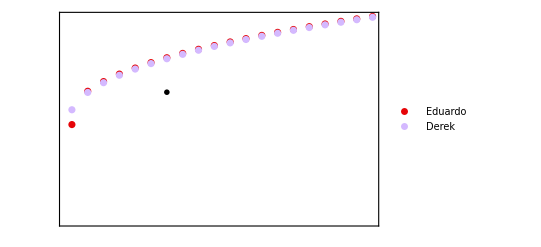

```mathematica
plot=ListPlot[{bla["mean"][[All,5]],bla2["mean"][[All,5]]},PlotRange->All,
Frame->True,
FrameStyle->BlackFrame,BaseStyle->texStyle,
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False]},{x,Range[4000,8000,1000]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False]},{x,Range[0,20,2]}],None}},
FrameLabel->{MaTeX["H"],MaTeX["\\langle |M| \\rangle "]},(*PlotMarkers->{{●,10},{▲,10}},*)PlotStyle->ColorData[60,"ColorList"],
PlotLegends->PointLegend[{"Eduardo","Derek"}],
Epilog->{Inset[MaTeX["m^2=-10\\quad \\lambda=5 \\quad N=16",Magnification->1.5],{07,5000},Scaled[{0.2,0.4}]]}]
```

```mathematica
Export[]
```

```mathematica
PointLegend[{Red,Green,Blue},{"red","green","blue"}]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,5},PlotLegends->SwatchLegend["Expressions"]]
```

```mathematica
ColorData["Pastel"]
```

ColorDataFunction[…]

```mathematica
ColorData[60,"ColorList"]
```

{RGBColor[0.90045, 0.0204013, 0.0301823],RGBColor[0.829938, 0.725154, 1],RGBColor[1, 0.511666, 0.141085],RGBColor[0.566842, 0.967407, 1],RGBColor[1, 0.926772, 0.151904],GrayLevel[1],RGBColor[0.759213, 0.886885, 0.319265],RGBColor[0.4, 0.8, 1],RGBColor[0.959274, 0.614496, 0.466316],RGBColor[0.790433, 0.450294, 1],RGBColor[0.895369, 0.716976, 0.346883],RGBColor[1, 0.0980392, 0.392157],RGBColor[1, 1, 0.392157],RGBColor[1, 0.4, 0.4],RGBColor[0.545876, 1, 0.558755],RGBColor[0.391867, 0.710414, 0.663966],RGBColor[1, 0.8, 0.4],RGBColor[1, 0.4, 0.4],RGBColor[1, 0, 1],RGBColor[0.563638, 0.606256, 0.935851],RGBColor[0.868772, 0.73959, 0.218616]}

```mathematica
ListPlot[{testData1,testData2,testData3},PlotMarkers->{{●,10},{▲,10},{■,10}}]
```

```mathematica
Dimensions[datalangev]
```

{20,1502,5}

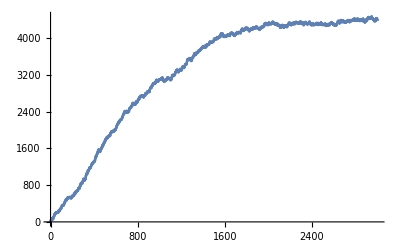

```mathematica
ListPlot@datalangev[[1,All,5]]
```

```mathematica
Inverse[{{g11,g12},{g21,g22}}]
```

{{g22/(-g12 g21+g11 g22),-g12/(-g12 g21+g11 g22)},{-g21/(-g12 g21+g11 g22),g11/(-g12 g21+g11 g22)}}

```mathematica
1/2{{1,1},{-1,1}}.{{0,gadv},{gret,g1}}. {{1,-1},{1,1}}
```

{{1/2 (g1+gadv+gret),1/2 (g1+gadv-gret)},{1/2 (g1-gadv+gret),1/2 (g1-gadv-gret)}}

```mathematica
1/2{{1,-1},{1,1}}.{{g11,g12},{g21,g22}}. {{1,1},{-1,1}}
```

{{1/2 (g11-g12-g21+g22),1/2 (g11+g12-g21-g22)},{1/2 (g11-g12+g21-g22),1/2 (g11+g12+g21+g22)}}